```mathematica
A={1+2I,3+4I};
B={5+6I,7+8I};

Dot[A,Conjugate[B]]
```

```mathematica
(1+2I)*(5-6I)+(3+4I)*(7-8I)
```

```mathematica
f[x_,y_,z_]:=Exp[z]+1/x+x*Exp[-y]; (*Define the function*)

D[f[x,y,z],x,x]/. x->x0 (*Find the second partial derivative at x=x0*)
```

```mathematica
f[x_,y_,z_]:=Exp[z]+1/x+x*Exp[-y]; (*Define the function*)

D[f[x,y,z],x,x] (*Second partial derivative with respect to x*)
D[f[x,y,z],x,y] (*Mixed partial derivative with respect to x and y*)
D[f[x,y,z],x,z] (*Mixed partial derivative with respect to x and z*)
D[f[x,y,z],y,y] (*Second partial derivative with respect to y*)
D[f[x,y,z],y,z] (*Mixed partial derivative with respect to y and z*)
D[f[x,y,z],z,z] (*Second partial derivative with respect to z*)
```

```mathematica
t=(1/(2Pi))*Integrate[Exp[a*x]*Exp[-I*n*x],{x,-Pi,Pi}]
```

```mathematica
(Sinh[(a-ⅈ n) π]/((a-ⅈ n) π)+Sinh[(a+ⅈ n) π]/((a+ⅈ n) π))*Cos[n*x]+(Sinh[(a-ⅈ n) π]/((a-ⅈ n) π)-Sinh[(a+ⅈ n) π]/((a+ⅈ n) π))*Sin[n*x]*I
```

```mathematica
expr=Sum[(2 a Cos[n x]+2 I n Sin[n x])/(a^2+n^2)-(2 I a Sin[n x]-2 n Cos[n x])/(a^2+n^2) π,{n,1,Infinity}];
expr=Simplify[expr];

exprFull=HoldForm[Sum[(2 a Cos[n x]+2 I n Sin[n x])/(a^2+n^2)-(2 I a Sin[n x]-2 n Cos[n x])/(a^2+n^2) π,{n,1,Infinity}]];
exprSimplified=HoldForm[-(π/2) (1-2 a Cot[x])];

Grid[{{"Full expression:",exprFull},{"Simplified expression:",exprSimplified}},Frame->All]
```

```mathematica
expr=(Sinh[(a-I n) π]/((a-I n) π)+Sinh[(a+I n) π]/((a+I n) π)) Cos[n x]+(Sinh[(a-I n) π]/((a-I n) π)-Sinh[(a+I n) π]/((a+I n) π)) Sin[n x] I;
expr=expr/. Sinh[(a-I n) π]/((a-I n) π)->(1/(π (a-I n))) (Exp[(a-I n) π]-1)/. Sinh[(a+I n) π]/((a+I n) π)->(1/(π (a+I n))) (Exp[(a+I n) π]-1);
expr=expr/. Sin[n x]->I Sinh[I n x]/. Cos[n x]->Cosh[I n x];
expr=ComplexExpand[expr];
expr=expr/. Cosh[n_ π]->((-1)^n+1)/2/. Sinh[n_ π]->((-1)^n-1)/2;
expr=Simplify[expr];
expr
```

```mathematica
(Sinh[(a-I n) π]/((a-I n) π)+Sinh[(a+I n) π]/((a+I n) π)) Cos[n x]+(Sinh[(a-I n) π]/((a-I n) π)-Sinh[(a+I n) π]/((a+I n) π)) Sin[n x] I
```

```mathematica
expr=(2 (-a Cos[n x]+a E^(a π) Cos[n (π+x)]-n Sin[n x]+E^(a π) n Sin[n (π+x)]))/((a^2+n^2) π);
expr/. n->1
```

```mathematica
expr=(Sinh[(a-I n) π]/((a-I n) π)+Sinh[(a+I n) π]/((a+I n) π)) Cos[n x]+(Sinh[(a-I n) π]/((a-I n) π)-Sinh[(a+I n) π]/((a+I n) π)) Sin[n x] I;
expr=expr/. Sinh[(a-I n) π]/((a-I n) π)->(1/(π (a-I n))) (Exp[(a-I n) π]-1)/. Sinh[(a+I n) π]/((a+I n) π)->(1/(π (a+I n))) (Exp[(a+I n) π]-1);
expr=expr/. Sin[n x]->I Sinh[I n x]/. Cos[n x]->Cosh[I n x];
expr=ComplexExpand[expr];
expr=expr/. Cosh[n_ π]->((-1)^n+1)/2/. Sinh[n_ π]->((-1)^n-1)/2;
expr=Simplify[expr];

simplifiedExpr=(-1)^n/(n^2+a^2) (a Cos[n x]-n Sin[n x]);

expr
```

```mathematica
expr=(Sinh[(a-I n) π]/((a-I n) π)+Sinh[(a+I n) π]/((a+I n) π)) Cos[n x]+(Sinh[(a-I n) π]/((a-I n) π)-Sinh[(a+I n) π]/((a+I n) π)) Sin[n x] I;
expr=expr/. Sinh[(a-I n) π]/((a-I n) π)->(1/(π (a-I n))) (Exp[(a-I n) π]-1)/. Sinh[(a+I n) π]/((a+I n) π)->(1/(π (a+I n))) (Exp[(a+I n) π]-1);
expr=expr/. Sin[n x]->I Sinh[I n x]/. Cos[n x]->Cosh[I n x];
expr=ComplexExpand[expr];
expr=expr/. Cosh[n_ π]->((-1)^n+1)/2/. Sinh[n_ π]->((-1)^n-1)/2;
expr=Simplify[expr];

simplifiedExpr=(2 a Cos[n x]+2 I n Sin[n x])/(a^2+n^2)-(2 I a Sin[n x]-2 n Cos[n x])/(a^2+n^2) π;

FullSimplify[expr-simplifiedExpr]
```

```mathematica
a=a;n=n;x=x;
Expr=ⅈ Sin[n x] ((2 a Cos[n π] Sin[a π]-2 n Cos[a π] Sin[n π])/(2 (a^2-n^2) π))+Cos[n x] ((2 a Cos[n π] Sin[a π]-2 n Cos[a π] Sin[n π])/(2 (a^2-n^2) π));

Simplify[Expr,Assumptions->Element[a,Reals]&&Element[n,Integers]]
```

```mathematica
(Sinh[(a-I n) Pi]/(a-I n) Pi+Sinh[(a+I n) Pi]/(a+I n) Pi) Cos[n x]+(Sinh[(a-I n) Pi]/(a-I n) Pi-Sinh[(a+I n) Pi]/(a+I n) Pi) Sin[n x] I
```

```mathematica
a
```

```mathematica
Sum[i^2,{i,1,n}]
```

```mathematica
(2 (1-2/3 Cos[2 x]))/π
```

```mathematica
Clear[n];
Clear[l];
Clear[a];
f=E^(a*x);
par=Pi;
fnP = (1/(2par))*(Integrate[f *Exp[-I*n*x],{x,-par,par}]);
fnN=fnP/.n->-n;
fo=(1/(2par))*(Integrate[f*Exp[-I*0*x],{x,-par,par}]);
Expr=ⅈ*Sin[n x] (fnP-fnN)+Cos[n x] (fnP+fnN);
fo+Activate[Sum][Simplify[Expr,Assumptions->Element[a,Reals]&&Element[n,Integers]&&Element[h,Reals]],{n,1,Infinity}];
Manipulate[Show[Plot[Sinh[a*Pi]/(a*Pi)(*+Activate[Sum][(2*(-1)^n*(a*Cos[n*x]-n*Sin[n*x])*Sinh[a*Pi])/((a^2+n^2)*Pi),{n,1,nMax}]*),{x,-Pi,Pi},PlotStyle->Red,PlotRange->All],Plot[E^(a*x),{x,-Pi,Pi},PlotStyle->Blue,PlotRange->All]],{{nMax,10,"n"},1,500,1,Appearance->"Labeled"},{{a,1,"a"},-10,10,Appearance->"Labeled"}]
```

```mathematica
Clear[n];
Clear[l];
Clear[a];
fo=0;
f=E^(a*x);
par=Pi;
fnP=(1/(2 par))*(Integrate[f*Exp[-I*n*x],{x,-par,par}]);
fnN=fnP/. n->-n;
Expr=I*Sin[n x] (fnP-fnN)+Cos[n x] (fnP+fnN);

Module[{n,l,a},fo=(1/(2 par))*(Integrate[f*Exp[-I*0*x],{x,-par,par}]);]
fo=fo;
Manipulate[Show[Plot[fo,{x,-Pi,Pi},PlotStyle->Red,PlotRange->All],Plot[E^(a*x),{x,-Pi,Pi},PlotStyle->Blue,PlotRange->All]],{{nMax,10,"n"},1,500,1,Appearance->"Labeled"},{{a,1,"a"},-10,10,Appearance->"Labeled"}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {-3.14146,0,h}.

NIntegrate::itraw: Raw object -3.14146 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.01324,0,h}.

NIntegrate::itraw: Raw object -3.01324 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-2.88501,0,h}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

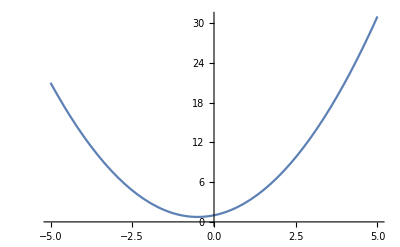

```mathematica
Clear[f,fo,par]

fo=0;

Module[{n,l,a,f,par},f=E^(a*x);
par=Pi;
fo=(1/(2 par))*(Integrate[f*Exp[-I*0*x],{x,-par,par}]);]

fo=fo;

Manipulate[Show[Plot[fo,{x,-Pi,Pi},PlotStyle->Red,PlotRange->All],Plot[E^(a*x),{x,-Pi,Pi},PlotStyle->Blue,PlotRange->All]],{{a,1,"a"},-10,10,Appearance->"Labeled"}]
```

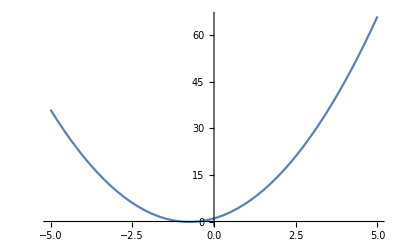

```mathematica
f[x_]:=a x^2+b x+c

Plot[f[x]/. {a->2,b->3,c->1},{x,-5,5}]
```

```mathematica
(*none piecewise function*)
Clear[n];
Clear[l];
Clear[a];
par=l;
f=Abs[Cos[Pi*x/par]];
M0[a_,x_,l_]=f;

muti=2;
fnP = (1/(muti*par))*(Integrate[f *Exp[-I*n*Pi*x/par],{x,-par,par}]);
fnN=fnP/.n->-n;
M1[a_,x_,l_]=(1/(muti*par))*(Integrate[f*Exp[-I*0*x],{x,-par,par}]);

Expr=ⅈ*Sin[n *Pi*x/par] (fnP-fnN)+Cos[n *Pi*x/par] (fnP+fnN);
M2[a_,n_,x_,l_]=Simplify[Expr,Assumptions->Element[a,Reals]&&Element[n,Integers]&&Element[h,Reals]];

Manipulate[Show[Plot[M1[a,x,l]+Activate[Sum][M2[a,n,x,l],{n,2,nMax}],{x,-2l,2l},PlotStyle->Red,PlotRange->All],Plot[M0[a,x,l],{x,-2l,2l},PlotStyle->Blue,PlotRange->All]],{{nMax,10,"n"},1,500,1,Appearance->"Labeled"},{{a,2.2,"a"},-10,10,Appearance->"Labeled"},{{l,2.2,"l"},0,Pi,Appearance->"Labeled"}]
```

```mathematica
(*piecewise function*)
Clear[n];
Clear[l];
Clear[a];
Clear[h];
par=h;
f=Piecewise[{{Sin[Pi*x/par],0<=x<par/2},{-Sin[Pi*x/par],par/2<x<=par}}];
M0[a_,x_,h_]=f;
muti=2;
fnP=(1/(muti*par))*(Integrate[f*Exp[-I*n*x*Pi/par],{x,-0,par},Assumptions->Element[par,Reals]]);
fnN=(1/(muti*par))*(Integrate[f*Exp[-I*-n*x*Pi/par],{x,-0,par},Assumptions->Element[par,Reals]]);
f1P=(1/(muti*par))*(Integrate[f*Exp[-I*1*x*Pi/par],{x,-0,par},Assumptions->Element[par,Reals]]);
f1N=(1/(muti*par))*(Integrate[f*Exp[-I*-1*x*Pi/par],{x,-0,par},Assumptions->Element[par,Reals]]);
fo=(1/(muti*par))*(Integrate[f*Exp[-I*0*x],{x,-0,par},Assumptions->Element[par,Reals]]);
(*fnN=fnP/. n->-n;
f1N=f1P/. 1->-1;*)
Expr=I*Sin[n*x*Pi/par] (fnP-fnN)+Cos[n*x*Pi/par] (fnP+fnN);
Expr1=I*Sin[1*x*Pi/par] (f1P-f1N)+Cos[1*x*Pi/par] (f1P+f1N);
M1[a_,h_]=fo;
M2[a_,n_,x_,h_]=Simplify[Expr,Assumptions->Element[a,Reals]&&Element[n,Integers]&&Element[h,Reals]];
M3[a_,n_,x_,h_]=Simplify[Expr1,Assumptions->Element[a,Reals]&&Element[n,Integers]&&Element[h,Reals]];
Manipulate[Show[Plot[M1[a,h]+M3[a,n,x,h]+Activate[Sum][M2[a,n,x,h],{n,2,nMax}],{x,0,h},PlotStyle->Red,PlotRange->All],Plot[M0[a,x,h],{x,0,h},PlotStyle->Blue,PlotRange->All]],{{nMax,10,"n"},1,1000,1,Appearance->"Labeled"},{{a,2.2,"a"},-10,10,Appearance->"Labeled"},{{h,2,"h"},0.1,10,Appearance->"Labeled"}]
```

```mathematica
Clear[n,l,a,h,x,par,muti,fnP,fnN,f1P,f1N,fo,Expr,Expr1,M1,M2,M3,integralFn,exprFn];

par=h;
f=Piecewise[{{Sin[Pi*x/par],0<=x<par/2},{-Sin[Pi*x/par],par/2<x<=par}}];
M0[a_,x_,h_]=f;
muti=2;

integralFn[n_,x_,h_,par_]:=(1/(muti*par))*(Integrate[f*Exp[-I*n*x*Pi/par],{x,-0,par},Assumptions->Element[par,Reals]]);
fnP=integralFn[n,x,h,par];
fnN=integralFn[-n,x,h,par];
f1P=integralFn[1,x,h,par];
f1N=integralFn[-1,x,h,par];
fo=integralFn[0,x,h,par];

exprFn[n_,x_,h_,par_,fnP_,fnN_]:=I*Sin[n*x*Pi/par] (fnP-fnN)+Cos[n*x*Pi/par] (fnP+fnN);
Expr=exprFn[n,x,h,par,fnP,fnN];
Expr1=exprFn[1,x,h,par,f1P,f1N];

M1[a_,h_]=fo;
M2[a_,n_,x_,h_]=Simplify[Expr,Assumptions->Element[a,Reals]&&Element[n,Integers]&&Element[h,Reals]];
M3[a_,n_,x_,h_]=Simplify[Expr1,Assumptions->Element[a,Reals]&&Element[n,Integers]&&Element[h,Reals]];

Manipulate[Show[Plot[M1[a,h]+M3[a,n,x,h]+Activate[Sum][M2[a,n,x,h],{n,2,nMax}],{x,0,h},PlotStyle->Red,PlotRange->All],Plot[M0[a,x,h],{x,0,h},PlotStyle->Blue,PlotRange->All]],{{nMax,10,"n"},1,1000,1,Appearance->"Labeled"},{{a,2.2,"a"},-10,10,Appearance->"Labeled"},{{h,2,"h"},0.1,10,Appearance->"Labeled"}]
```

Symbol::argx: Symbol called with 2 arguments; 1 argument is expected.

Set::write: Tag Symbol in Symbol[a,Positive][0] is Protected.

SetDelayed::write: Tag Symbol in Symbol[a,Positive][n_] is Protected.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.14146,-π,π}.

NIntegrate::itraw: Raw object -3.14146 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.01324,-π,π}.

NIntegrate::itraw: Raw object -3.01324 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-2.88501,-π,π}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.14146,-π,π}.

NIntegrate::itraw: Raw object -3.14146 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.01324,-π,π}.

NIntegrate::itraw: Raw object -3.01324 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-2.88501,-π,π}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.14146,-π,π}.

NIntegrate::itraw: Raw object -3.14146 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.01324,-π,π}.

NIntegrate::itraw: Raw object -3.01324 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-2.88501,-π,π}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.14146,-π,π}.

NIntegrate::itraw: Raw object -3.14146 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {-3.01324,-π,π}.

NIntegrate::itraw: Raw object -3.01324 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {-2.88501,-π,π}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

SetDelayed::write: Tag Power in ⅇ^(a x)[a_] is Protected.

PacletObject[…]

PacletObject[…]

PacletObject[…]

«1 more identical outputs»